# Example: Type IIB on T^6/ℤ_6

```mathematica
Quit[]
```

As an example consider Type IIB supergravity compactified on the Riemann-flat manifold T^6/ℤ_8 as example,with ℤ_8 generated by the action  z^(->)->D_g z^(->)+(b^(->))_g  with
      D_g=(0 | -1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)  ,  (b^(->))_g=(0
0
0
0
0
0
1/8) .
We will choose the spin lift of D_g such that σ_g=1/2.

Using the function GetGroup we get the eight elements of ℤ_8 generated by g (we show the first three elements).

```mathematica
<<CasimirRFM`
```

```mathematica
gens={{({{0, 0, 0, -1, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}}),{0,0,0,0,0,1/8},1/2}};
Γ=GetGroup[gens];
Length[Γ]
Γ[[;;3]]//Map[MatrixForm,#,{2}]&
```

8

{{(0 | 0 | 0 | -1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(0
0
0
0
0
1/8),1/2},{(0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(0
0
0
0
0
1/4),0},{(0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1),(0
0
0
0
0
3/8),1/2}}

The most general metric invariant under this ℤ_8 action contains 5 moduli and there are 4 distinct spin structures on T^6 compatible with the group action and
spin lift. To get the most general form of the spin structure vector h^(->) we evaluate SpinStructures[gens][“GeneralForm”], and to get a list of all allowed spin structures we evaluate SpinStructures[gens][“Allowed”]. We find that we must make the same choice for all of the first four directions, and that the last direction must be necessarily zero.

```mathematica
MatrixForm/@{G=GetInvariantMetric[gens][[3]]}
SpinStructures[gens]["GeneralForm"]
SpinStructures[gens]["Allowed"]
```

{(c_4 | c_5 | 0 | -c_5 | 0 | 0
c_5 | c_4 | c_5 | 0 | 0 | 0
0 | c_5 | c_4 | c_5 | 0 | 0
-c_5 | 0 | c_5 | c_4 | 0 | 0
0 | 0 | 0 | 0 | c_3 | c_2
0 | 0 | 0 | 0 | c_2 | c_1)}

{h_1,h_1,h_1,h_1,h_5,0}

{{0,0,0,0,0,0},{0,0,0,0,1/2,0},{1/2,1/2,1/2,1/2,0,0},{1/2,1/2,1/2,1/2,1/2,0}}

The massless spectrum of Type IIB contains the graviton, two scalars, two 2-forms and one self-dual 4-form (G,ϕ,C_0,B_2,C_2,C_4), in the bosonic sector, and two Weyl spinors and two gravitinos, in the fermionic sector (χ_a^(μ,1),χ_a^(μ,2),λ_α^1,λ_α^2).

```mathematica
spectrum =
<|"Bosons"->{
<|"Type"->"Graviton"|>,
<|"Type"->"Scalar","Multiplicity"->2|>,
<|"Type"->"Form","Rank"->2,"Multiplicity"->2|>,
<|"Type"->"Form","Rank"->4,"SelfDual"->True|>
},
"Fermions"->{
<|"Type"->"Spinor","Weyl"->True,"Multiplicity"->2|>,
<|"Type"->"Gravitino","Weyl"->True,"Multiplicity"->2|>
}|>; (* Type IIB *)
TraceBosons[spectrum["Bosons"],#,10]&/@Γ
TraceFermions[spectrum["Fermions"],#,10]&/@Γ
```

{24,32,24,0,24,32,24,128}

{-16 √2,32,-16 √2,0,-16 √2,32,-16 √2,128}

For the identity element, both traces equal 128, reproducing the matching numbers of physical bosonic and fermionic degrees of freedom in Type IIB supergravity. 
The same results are obtained using the shorthand notation introduced in Section 2.5.

```mathematica
TraceBosons[{1,0,0,2,2,4I},#,10]&/@Γ
TraceFermions[{3/2,3/2,1,1}I,#,10]&/@Γ
```

{24,32,24,0,24,32,24,128}

{-16 √2,32,-16 √2,0,-16 √2,32,-16 √2,128}

The Casimir potential is a function of the 5 moduli {c_1,c_2,c_3,c_4,c_5}. We can evaluate it, for example, at the point in moduli space that reduces the metric G to the identity matrix, for two different choices of spin structure h^(->). The numerical values below use the default truncation target ε=10^-4.

```mathematica
MatrixForm/@{G/.{Subscript[c, 2]->0,Subscript[c, 5]->0,Subscript[c, a_]:>1}}
```

{(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
CasimirPotential[10,Γ,spectrum,{0,0,0,0,0,0},G,{Subscript[c, 2]->0,Subscript[c, 5]->0,Subscript[c, a_]:>1}]
```

98697.9

```mathematica
CasimirPotential[10,Γ,spectrum,{1/2,1/2,1/2,1/2,0,0},G,{Subscript[c, 2]->0,Subscript[c, 5]->0,Subscript[c, a_]:>1}]
```

51872.6

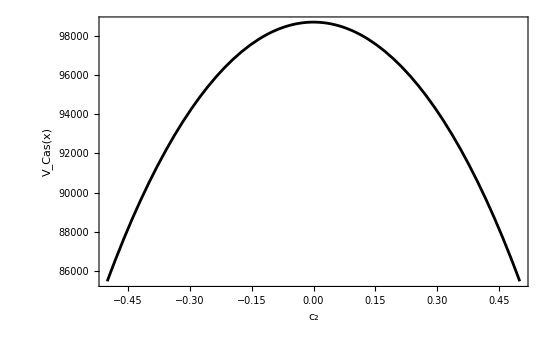

```mathematica
Plot[{CasimirPotential[10,Γ,spectrum,{0,0,0,0,0,0},G,{Subscript[c, 2]->x,Subscript[c, 5]->0,Subscript[c, a_]:>1}]},{x,-0.5,0.5},PlotStyle->{Black},
Frame->True,FrameLabel->{Style["c_2",16,FontFamily->"Times"], Style["V_Cas(x)",16,FontFamily->"Times"]}]
```

We can visualize Casimir branes by plotting the Casimir energy density along a given plane.  
For example, there are two Casimir branes associated with the generator (and first element of Γ).

```mathematica
CasimirBranes@Γ[[1]]
```

{{0,0,0,0,z[5],z[6]},{1/2,1/2,1/2,1/2,z[5],z[6]}}

The two branes are localised on the first four directions of T^6 and wrapping the last two. 
In order to visualise both branes, we can change coordinates as

u_1=z_1+z_2+z_3+z_4
u_2=z_1-z_2+z_3-z_4
u_3=z_3-z_2
u_4=z_4-z_3

so that the two Casimir branes are located at {0,0,0,0} and {1/2,0,0,0} and we can plot the Casimir energy density along the u_1-u_2 plane, with u_3=u_4=0.

```mathematica
R=1/4({{1, 1, 1, 1, 0, 0}, {1, -1, 1, -1, 0, 0}, {1, 1, -1, -1, 0, 0}, {1, -1, -1, 1, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 4}});(*Rotation matrix*)
R.#&/@(CasimirBranes@Γ[[1]])
```

{{0,0,0,0,z[5],z[6]},{1/2,0,0,0,z[5],z[6]}}

This is also a case in which parallelizing the computation is particularly useful. 
We can first generate a ParallelTable with 

	(i) the Casimir energy density from element Γ[[1]] 
	(ii) the boson contribution to the energy density from element Γ[[1]]
	(iii) the fermion contribution to the energy density from element Γ[[1]]

and then plot them using ListPlot3D. This also has the advantage that we can style the plot without having to evaluate the functions every time.

```mathematica
LaunchKernels[];
ParallelEvaluate[<<CasimirRFM`];
DistributeDefinitions[Γ,spectrum,G,R];
```

```mathematica
CBranes=ParallelTable[{u1,u2,CasimirEnergyDensity[10,{Γ[[1]]},spectrum,{1/2,1/2,1/2,1/2,0,0},G,{Subscript[c, 2]->0,Subscript[c, 5]->0,Subscript[c, a_]:>1},Inverse[R].{u1,u2,0,0,0,0}]},{u1,-0.25,0.75,0.005},{u2,-0.25,0.25,0.005}]//Flatten[#,1]&;
```

```mathematica
CBranesBosons=ParallelTable[{u1,u2,CasimirEnergyDensity[10,{Γ[[1]]},KeyTake[spectrum,"Bosons"],{1/2,1/2,1/2,1/2,0,0},G,{Subscript[c, 2]->0,Subscript[c, 5]->0,Subscript[c, a_]:>1},Inverse[R].{u1,u2,0,0,0,0}]},{u1,-0.25,0.75,0.005},{u2,-0.25,0.25,0.005}]//Flatten[#,1]&;
```

```mathematica
CBranesFermions=ParallelTable[{u1,u2,CasimirEnergyDensity[10,{Γ[[1]]},KeyTake[spectrum,"Fermions"],{1/2,1/2,1/2,1/2,0,0},G,{Subscript[c, 2]->0,Subscript[c, 5]->0,Subscript[c, a_]:>1},Inverse[R].{u1,u2,0,0,0,0}]},{u1,-0.25,0.75,0.005},{u2,-0.25,0.25,0.005}]//Flatten[#,1]&;
```

```mathematica
CBraneStyle={ViewPoint->2{1.5,-1.5,0.5},BoxRatios->{1,1,2/3},TicksStyle->Directive[12],
ColorFunction->(ColorData["BlueGreenYellow"]),Mesh->None,ImageSize->500};
```

```mathematica
ListPlot3D[CBranes,PlotRange->10^9{-2,2},AxesLabel->(Style[#,18,FontFamily->"Times"]&/@{"u_1","u_2","ρ_Cas"}),Evaluate[CBraneStyle]]
```

-Graphics3D-

```mathematica
GraphicsRow[{
ListPlot3D[CBranesBosons,PlotRange->10^9{-1,1},AxesLabel->(Style[#,18,FontFamily->"Times"]&/@{"u_1","u_2","ρ_Cas"}),Evaluate[CBraneStyle]],
ListPlot3D[CBranesFermions,PlotRange->10^9{-1,1},AxesLabel->(Style[#,18,FontFamily->"Times"]&/@{"u_1","u_2","ρ_Cas"}),Evaluate[CBraneStyle]]
},ImageSize->750]
```

-Graphics-